27.9602

13.823

0.02

4.20973

-0.00150796

1.18305×10^-7

0.707107

0.55

10.4458

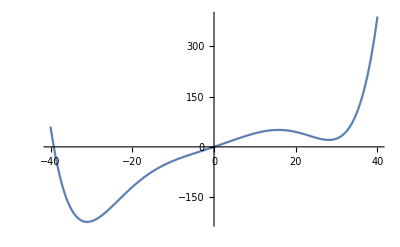

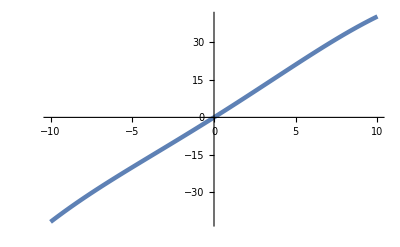

{{W→InterpolatingFunction[{{-50., 50.}, {0., 10.}}, <>]}}

-Graphics3D-

-Graphics3D-

-Graphics3D-

General::munfl: 1.49984×10^-307 0.144092 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -7.2958×10^-308 (-0.144092) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.20619×10^-308 (-0.144092) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

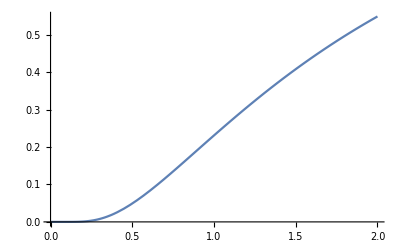

General::munfl: 2.22654×10^-308-3.33906×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.71446×10^-306-4.71723×10^-306 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.24352×10^-308 (-0.144092) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

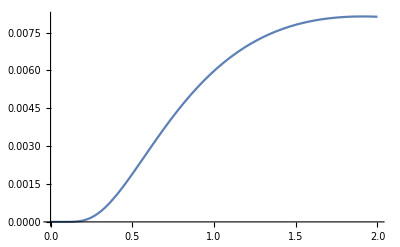

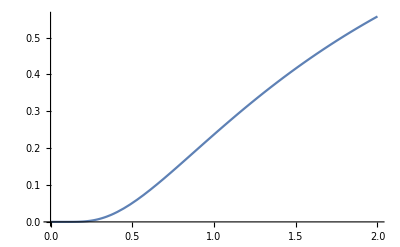

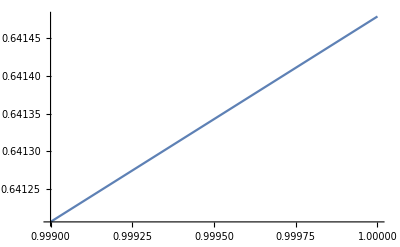

```mathematica
kappa = (2 * Pi)* (4.44 +1*0.01)
gamma =(2 * Pi) * (2.30 -1*0.1)
T = 0.02(*temperature in Kelvin*)
aalpha[t_]:=(0.51-0.4*0.004) *(kappa + gamma)
Delta =(2 * Pi)* (0.70 -0.3* 0.10)
K = -(2 * Pi)* (0.0002 + 1* 0.00004)
nT = 0.5 * Coth[ 0.319/(2T)] - 0.5
sigmaSP = Sqrt[nT + 1/2]
b=1.1Sqrt[0.25]
U[Q_] := (2/(aalpha[t] + (kappa + gamma)/2))* (0.25*( (kappa/2 + gamma/2)^2 + Delta^2 - aalpha[t]^2)* Q^2 + (3/2)* Delta *K* Q^4 + 3 K^2 Q^6) + Sqrt[2 kappa]* b *Q
Diff = 0.5*(kappa + gamma)*(nT + 1/2)
Plot[U[Q], {Q, -40, 40},LabelStyle -> FontSize ->7,TicksStyle -> Directive[7],PlotRange->All]
Plot[U[Q], {Q, -10, 10},LabelStyle -> FontSize ->12,PlotStyle -> Thickness[0.008], PlotRange->All]
S=NDSolve[{D[W[Q,t],t] == D[W[Q,t],Q]*D[U[Q],Q] +W[Q,t]*D[U[Q],Q,Q]+ Diff * D[W[Q,t],Q,Q], W[Q,0] == (1/(Sqrt[2 Pi] sigmaSP)) Exp[-Q^2/(2 sigmaSP^2)], W[50,t]== 0, W[-50,t]== 0}, W, {Q,-50,50},{t,0,10}]
WW[Q_,t_] :=Evaluate[W[Q,t]/.S] 
Plot3D[WW[Q,t],{Q,-35,-20},{t,0,10},LabelStyle -> FontSize ->12,PlotRange->All]
Plot3D[WW[Q,t],{Q,20,35},{t,0,10},LabelStyle -> FontSize ->12,PlotRange->All]
Plot3D[WW[Q,t],{Q,-6.5,6.5},{t,0,2},LabelStyle -> FontSize ->12,PlotRange->All]
P[t_] := Integrate[WW[Q,t], {Q,-7.5,7.5}]
Pleft[t_] := Integrate[WW[Q,t], {Q,-50,-7.5}]
Pright[t_] := Integrate[WW[Q,t], {Q,7.5,50}]
Pdetected[t_] := 1 - P[t]
Plot[Pleft[t], {t,0,2},LabelStyle -> FontSize ->12]
Plot[Pright[t], {t,0,2},LabelStyle -> FontSize ->12]
Plot[Pdetected[t], {t,0,2},LabelStyle -> FontSize ->12]
Plot[(1-Exp[-(0.703^(1/(1 + 0.12 nbar)))*nbar])*0.744 + 0.256, {nbar, 0.999, 1}, PlotRange->All]
(*Plot[{P[t]/P[1.7],Exp[-1.1(t-0.15)]}, {t,0,4}]
Plot[-Log[P[t]]/(b^2 (t-1.2)), {t,0,4}] *)
 (* note from this plot that Pdark is around 2.5 for a 1 microsec pulse, which is what is observed experimentally*)
```